```mathematica
Hmb[a_?NumberQ,μ0_?NumberQ,Δ0_?NumberQ,V0_?NumberQ,α0_?NumberQ,dim_?IntegerQ]:=Block[{t=25/a^2,μ=μ0,α=α0/(2a),Vz=V0,Δ11=Δ0,Δ12=Δ0,H11,H12,H22,ϵ=1},H11=KroneckerProduct[PauliMatrix[3],KroneckerProduct[PauliMatrix[0],-t*(SparseArray[{Band[{1,2}]->1,Band[{2,1}]->1},{dim,dim}])+(-μ+2*t)IdentityMatrix[dim,SparseArray]]+KroneckerProduct[PauliMatrix[2],I*α*(SparseArray[{Band[{1,2}]->-1,Band[{2,1}]->1},{dim,dim}])]]+KroneckerProduct[PauliMatrix[0],KroneckerProduct[PauliMatrix[3],Vz*IdentityMatrix[dim,SparseArray]]]+KroneckerProduct[PauliMatrix[1],KroneckerProduct[PauliMatrix[0],Δ11*IdentityMatrix[dim,SparseArray]]];H22=KroneckerProduct[PauliMatrix[3],KroneckerProduct[PauliMatrix[0],-t*(SparseArray[{Band[{1,2}]->1,Band[{2,1}]->1},{dim,dim}])+(ϵ-μ+2*t)IdentityMatrix[dim,SparseArray]]+KroneckerProduct[PauliMatrix[2],I*α*(SparseArray[{Band[{1,2}]->-1,Band[{2,1}]->1},{dim,dim}])]]+KroneckerProduct[PauliMatrix[0],KroneckerProduct[PauliMatrix[3],Vz*IdentityMatrix[dim,SparseArray]]]+KroneckerProduct[PauliMatrix[1],KroneckerProduct[PauliMatrix[0],Δ11*IdentityMatrix[dim,SparseArray]]];H12=KroneckerProduct[PauliMatrix[1],KroneckerProduct[PauliMatrix[0],Δ12*IdentityMatrix[dim,SparseArray]]];Chop@ArrayFlatten[{{H11,H12},{H12,H22}}]]
```

```mathematica
Hmbp[μ0_,Δ0_,α0_,V0_]:=Block[{H11,H12,H22,H,Hmb22,Hmb11,Hmb12,η=25,k,μ=μ0,V=V0,α=α0,Δ=Δ0,Δc=.2,Hp,ϵ=0,sl,u=.5},H11=(η k^2 -μ)*IdentityMatrix[2]+V PauliMatrix[3]-α k PauliMatrix[2];H12=Δ IdentityMatrix[2];H22=-(η k^2 -μ)*IdentityMatrix[2]+V PauliMatrix[3]+α k PauliMatrix[2];H=ArrayFlatten[{{H11,H12},{H12,H22}}];Hmb22=ArrayFlatten[{{(η k^2 -(μ-ϵ))*IdentityMatrix[2]+V PauliMatrix[3]-α k PauliMatrix[2],Δ IdentityMatrix[2]},{Δ IdentityMatrix[2],-(η k^2 -(μ-ϵ))*IdentityMatrix[2]+V PauliMatrix[3]+α k PauliMatrix[2]}}];Hmb11=H;Hmb12=KroneckerProduct[PauliMatrix[1],IdentityMatrix[2]]Δc;Hp=ArrayFlatten[{{Hmb11,Hmb12},{Hmb12,Hmb22}}];sl=Eigenvalues[Hp];ListLinePlot[Transpose@Table[sl,{k,-u,u,.01}],DataRange->{-u,u},PlotRange->{{-u,u},{0,2}},PlotStyle->{Blue,LightBlue,Red,LightRed},PlotLabel->sl[[5]]/.k->0]]
```

```mathematica
Manipulate[Hmbp[μx,Δx,αx,Vx],{μx,0,2},{Δx,0,0.2},{αx,1,3},{Vx,0,2},SaveDefinitions->True]
```

```mathematica
data=Block[{vzm=1,vzstep=0.02,μ=0.1,α=2,Δ=0.2},ParallelTable[First@Sort[Select[Re@Eigenvalues[Hmb[1,μ,Δ,vz,α,3000],-20,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞}],#>0&]],{vz,0,vzm,vzstep}]]
```

$Aborted

```mathematica
data=Block[{vzm=1,vzstep=0.02,μ=0.1,α=2,Δ=0.2},ParallelTable[{vz,Min@Abs@Eigenvalues[Hmb[1,μ,Δ,vz,α,3000],-20,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞}]},{vz,0,vzm,vzstep}]]
```

{{0.,0.183305},{0.02,0.168786},{0.04,0.148913},{0.06,0.128916},{0.08,0.108918},{0.1,0.088922},{0.12,0.0689275},{0.14,0.0489371},{0.16,0.0289591},{0.18,0.00906687},{0.2,1.46765×10^-10},{0.22,3.24556×10^-18},{0.24,2.22027×10^-15},{0.26,8.06606×10^-16},{0.28,5.15333×10^-16},{0.3,9.37392×10^-16},{0.32,6.20041×10^-17},{0.34,1.68691×10^-15},{0.36,2.57346×10^-15},{0.38,1.08775×10^-15},{0.4,6.74942×10^-16},{0.42,1.40315×10^-15},{0.44,1.09174×10^-15},{0.46,2.20354×10^-15},{0.48,1.49365×10^-15},{0.5,1.24246×10^-15},{0.52,2.28161×10^-16},{0.54,8.53456×10^-17},{0.56,8.35001×10^-17},{0.58,1.44592×10^-16},{0.6,4.84901×10^-17},{0.62,2.59744×10^-17},{0.64,1.32033×10^-15},{0.66,1.0514×10^-16},{0.68,3.51146×10^-16},{0.7,4.13521×10^-16},{0.72,7.45994×10^-16},{0.74,1.12041×10^-15},{0.76,7.75079×10^-15},{0.78,1.74471×10^-14},{0.8,3.71297×10^-14},{0.82,7.49228×10^-14},{0.84,1.52402×10^-13},{0.86,2.85739×10^-13},{0.88,5.01973×10^-13},{0.9,7.98483×10^-13},{0.92,1.04111×10^-12},{0.94,8.40225×10^-13},{0.96,5.97857×10^-13},{0.98,8.20776×10^-16},{1.,3.33277×10^-15}}

```mathematica
data2=Block[{vzm=1,vzstep=0.01,μ=0.1,α=2,Δ=0.2},ParallelTable[First@Sort[Select[Re@Eigenvalues[SparseArray@Hc[1,μ,Δ,vz,α,3000],-10,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞}],#>0&]],{vz,0,vzm,vzstep}]]
```

```mathematica
Dynamic[vz]
```

```mathematica
data//Length
```

51

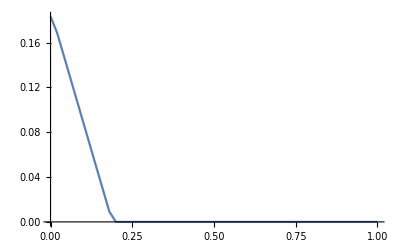

```mathematica
ListLinePlot[data,PlotRange->Full]
```

### Δ12=.1meV

```mathematica
delta120p1=Import[NotebookDirectory[]<>"\\deltac0.1.dat"];
```

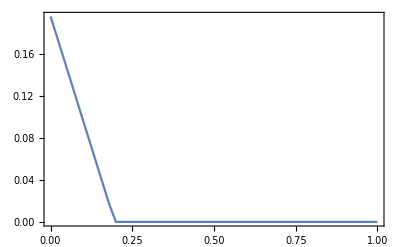
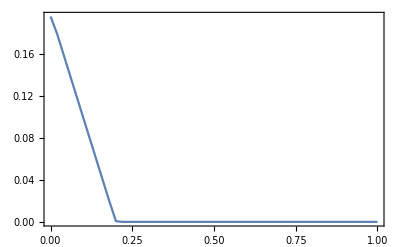
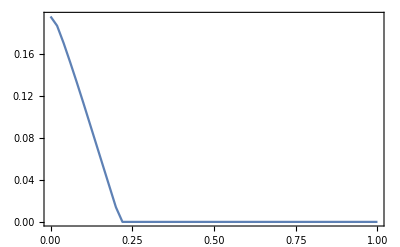
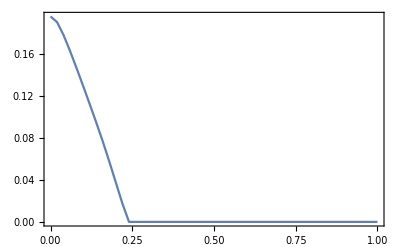
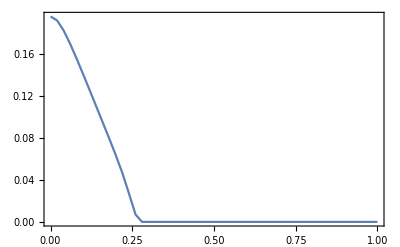
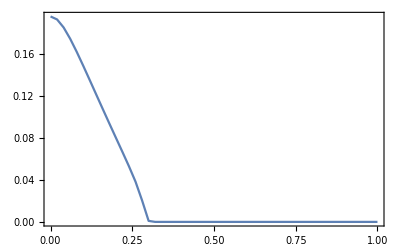
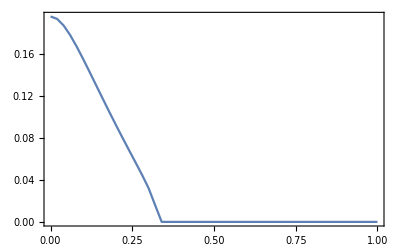
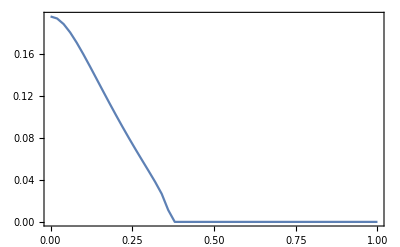

```mathematica
ListLinePlot[#,PlotRange->Full,Frame->True,DataRange->{0,1}]&/@delta120p1
```

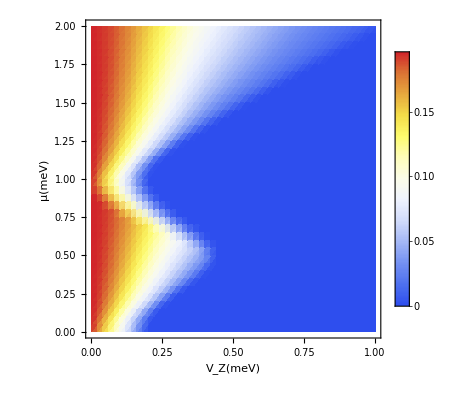

```mathematica
ListDensityPlot[delta120p1,PlotLegends->Automatic,ColorFunction->"TemperatureMap",DataRange->{{0,1},{0,2}},FrameLabel->{"V_Z(meV)","μ(meV)"}]
```

### Δ12=.2meV

```mathematica
delta120p2=Import[NotebookDirectory[]<>"\\deltac0.2.dat"];
```

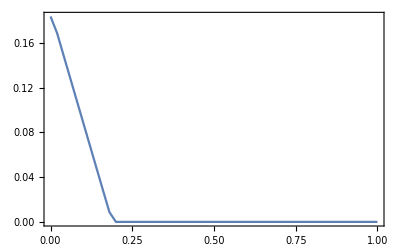
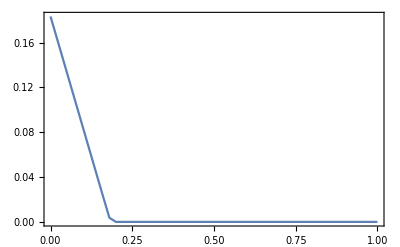
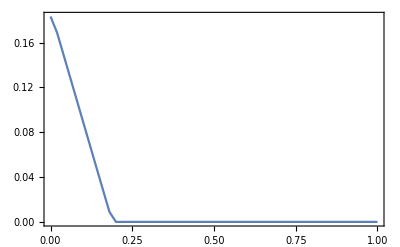
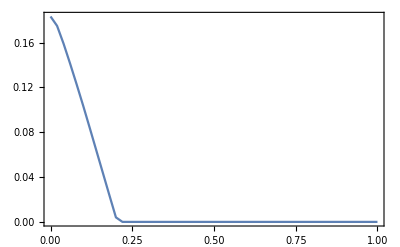
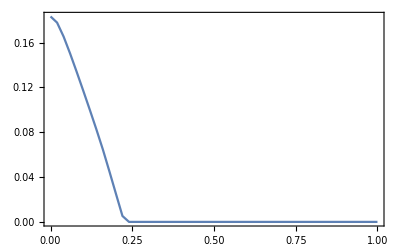
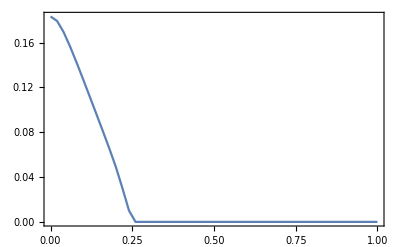
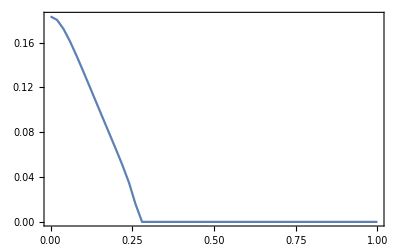
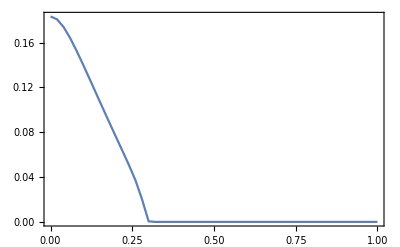

```mathematica
ListLinePlot[#,PlotRange->Full,Frame->True,DataRange->{0,1}]&/@delta120p2
```

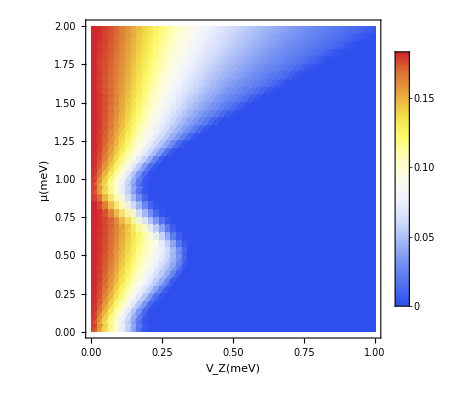

```mathematica
ListDensityPlot[delta120p2,PlotLegends->Automatic,ColorFunction->"TemperatureMap",DataRange->{{0,1},{0,2}},FrameLabel->{"V_Z(meV)","μ(meV)"}]
```

```mathematica
bottom=Import[NotebookDirectory[]<>"\\b.dat"];
```

```mathematica
upper=Import[NotebookDirectory[]<>"\\u.dat"];
```

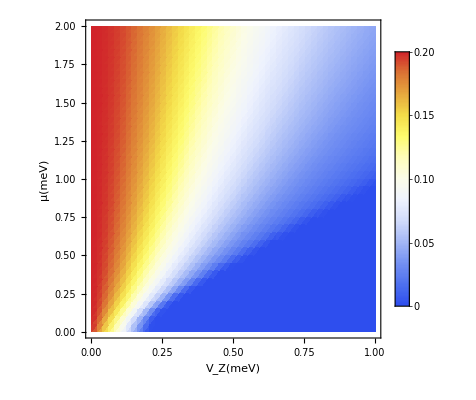

```mathematica
ListDensityPlot[bottom,PlotLegends->Automatic,ColorFunction->"TemperatureMap",DataRange->{{0,1},{0,2}},FrameLabel->{"V_Z(meV)","μ(meV)"}]
```

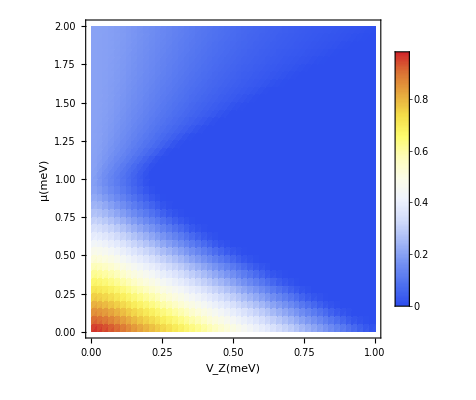

```mathematica
ListDensityPlot[upper,PlotLegends->Automatic,ColorFunction->"TemperatureMap",DataRange->{{0,1},{0,2}},FrameLabel->{"V_Z(meV)","μ(meV)"},PlotRange->Full]
```

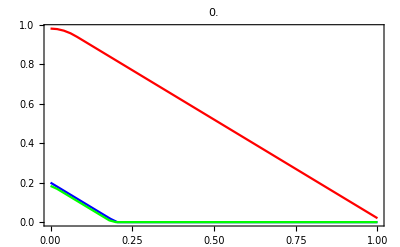
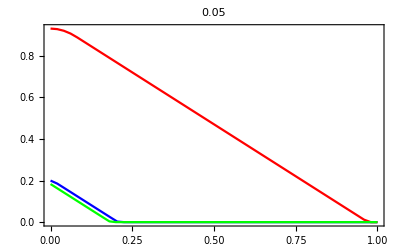
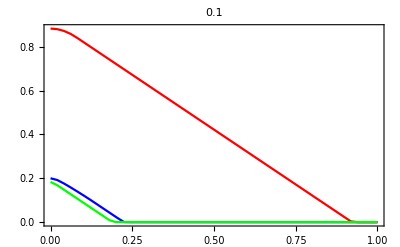
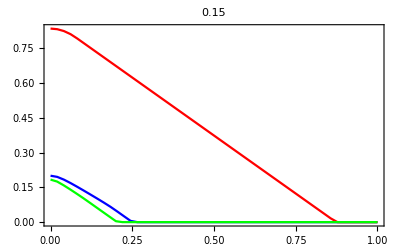
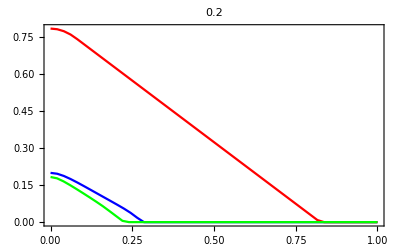
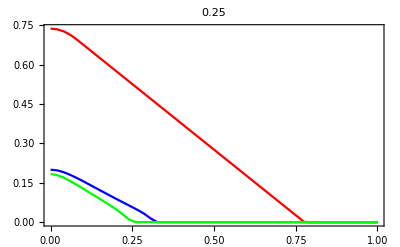
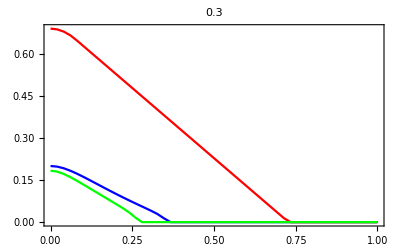
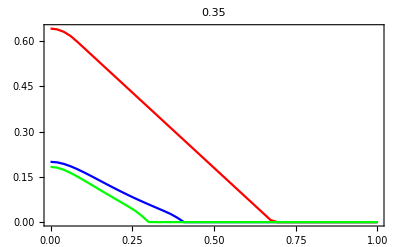

```mathematica
MapThread[ListLinePlot[{#1,#2,#3},PlotRange->Full,Frame->True,DataRange->{0,1},PlotStyle->{Blue,Red,Green},PlotLabel->ToString@#4]&,{bottom,upper,delta120p2,Range[0,2,.05]}]
```

### Δ12=.3meV

```mathematica
delta120p3=Import[NotebookDirectory[]<>"\\deltac0.3.dat"];
```

```mathematica
ListLinePlot[#,PlotRange->Full,Frame->True,DataRange->{0,1}]&/@delta120p3
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListDensityPlot[delta120p3,PlotLegends->Automatic,ColorFunction->"TemperatureMap",DataRange->{{0,1},{0,2}},FrameLabel->{"V_Z(meV)","μ(meV)"}]
```

-Graphics-

```mathematica
Grid@{{Out[407],Out[408],Out[409]}}
```

-Graphics- | -Graphics- | -Graphics-